# GettingStarted

This notebook provides a quick introduction to the Mathematica package TuGames.

How to load the package | Plotting the Core, Strong Epsilon Core, and the Weber Set in 3D
Defining a Game | Plotting Kernel Catchers in 3D
Some Solution Concepts and Game Properties | Animation of Geometric Properties of the Kernel/Nucleous

The forthcoming section illustrates the usage of some useful commands of TuGames.

## TuGames Getting Started

#### Loading the Package

```mathematica
Needs["TUG`"]
```

===================================================

Loading Package 'TuGames' for Unix

===================================================

TuGames V3.1.4 by Holger I. Meinhardt

Release Date: 31.05.2024

Program runs under Mathematica Version 12.0 or later

Version 12.x or higher is recommended

===================================================

===================================================

Package 'TuGames' loaded

===================================================

#### Defining a Game

We define a four-person TU-game that we have borrowed from  D. Mueller (2019; Exp.6.6, p. 510).

```mathematica
vec={0,0,0,0,0,7,7,0,0,0,0,0,0,0,0,8}
```

{0,0,0,0,0,7,7,0,0,0,0,0,0,0,0,8}

```mathematica
Length[vec]
```

16

```mathematica
T={1,2,3,4}
```

{1,2,3,4}

```mathematica
ExpGame12=DefineGame[T,vec];
```

#### Some Solutions Concepts and Game Properties

First, we compute the vertices of the core.

```mathematica
crv=CddGmpVerticesCore[ExpGame12]
```

{{6,1,1,0},{7,0,0,1},{7,0,1,0},{7,1,0,0},{8,0,0,0}}

An element of the kernel can be found by

```mathematica
ker=Kernel[ExpGame12]
```

{7,1/3,1/3,1/3}

In the next step, we try to find out whether there exists a line segment within the kernel solution.

```mathematica
kerv=KernelVertices[ExpGame12]
```

{{7,1/3,1/3,1/3}}

The Shapley value is computed by

```mathematica
shv=ShapleyValue[ExpGame12]
```

{19/6,2,2,5/6}

In contrast, the Harsanyi value as an exposed solution of the Harsanyi set can be computed by

```mathematica
harv=HarsanyiValue[ExpGame12]
```

{19/6,2,2,5/6}

The nucleolus by

```mathematica
mnuc=ModifiedNucleolus[ExpGame12]
```

{7,1/3,1/3,1/3}

This function should not be confused with the modiclus. It only indicates that a different algorithm has been implemented to compute the nucleolus.

And the pre-nucleolus via

```mathematica
pn=PreNucleolus[ExpGame12]
```

{7,1/3,1/3,1/3}

Notice that the game is zero-monotonic, hence, the nucleolus and the pre-nucleolus coincide.

In addition, we are able to compute the modiclus of the game by

```mathematica
mnc=Modiclus[ExpGame12]
```

{13/2,1/2,1/2,1/2}

If the retrieved solution is indeed the modiclus can be checked out with

```mathematica
IsModiclusQ[ExpGame12,mnc]
```

True

Furthermore, an element of the modified pre-kernel can be computed through

```mathematica
mpk=ModPreKernel[ExpGame12]
```

{2,2,2,2}

and that is checked out by

```mathematica
IsModPreKernelQ[ExpGame12,mpk]
```

{True}

```mathematica
IsModPreKernelQ[ExpGame12,mnc]
```

{True}

Similar, an element of the proper modified pre-kernel can be computed through

```mathematica
pmpk=ProperModPreKernel[ExpGame12]
```

{13/2,1/2,1/2,1/2}

This solution is verified with the help of

```mathematica
IsProperModPreKernelQ[ExpGame12,pmpk]
```

{True}

```mathematica
IsProperModPreKernelQ[ExpGame12,mpk]
```

{False}

Convexity we verify by

```mathematica
ConvexQ[ExpGame12]
```

False

and average-convexity through

```mathematica
AverageConvexQ[ExpGame12]
```

False

Core existence can be retrieved by

```mathematica
CoreQ[ExpGame12]
```

True

In the next step, we consider the Lorenz solution. For that reason we introduce the equalitarian allocation by

```mathematica
fc=Table[v[T]/Length[T],{i,1,Length[T]}]
```

{2,2,2,2}

First, we find out which options are supported by the function that computes the Lorenz solution for us. This is accomplished by

```mathematica
Options[LorenzSolution]
```

{DigitPrecision→20,RationalApproximate→True,Method→Automatic}

Now, we retrieve the Lorenz solution via

```mathematica
lr=LorenzSolution[ExpGame12,DigitPrecision->20,RationalApproximate->False]
```

{6.000000000038424699,0.99999999998078765038,0.99999999998078765038,0}

and computing then the Euclidean distance to the equalitarian allocation through

```mathematica
EuclidianDistance[lr,fc]
```

4.69042

which is a function provided by the package “TuGamesAux”. However, if more precision is required one should use the Mathematica built-in function

```mathematica
EuclideanDistance[lr,fc]
```

4.690415759864390422

In the next step, we vary the working precision to compute the Lorenz solution from 20 digits to 10.

```mathematica
lr=LorenzSolution[ExpGame12,DigitPrecision->10,RationalApproximate->False]
```

{5.99999999,1.000000004,1.000000004,0}

Rather than returning a floating point number, the function can also retrieve a rational approximation as a solution.

```mathematica
lr=LorenzSolution[ExpGame12,RationalApproximate->True]
```

{6,1,1,0}

Again, we compute the Euclidean distance with

```mathematica
EuclidianDistance[lr,fc]
```

4.69042

```mathematica
EuclideanDistance[lr,fc]
```

√22

Now, we introduce a second allocation that was introduced  in the above example by Table 6.13 within the book of Mueller (2019).

```mathematica
x2={13/2,1/2,1,0}
```

{13/2,1/2,1,0}

and an additional core allocation that is given by

```mathematica
lcb={749/100,1/150,1/150,149/300}
```

{749/100,1/150,1/150,149/300}

Finally, we show how all marginal contributions can be computed.

```mathematica
mrgv=MargValue[ExpGame12]
```

{{0,7,-7,8},{0,7,8,-7},{0,-7,7,8},{0,8,7,-7},{0,0,8,0},{0,8,0,0},{7,0,-7,8},{7,0,8,-7},{0,0,0,8},{8,0,0,0},{0,0,8,0},{8,0,0,0},{7,-7,0,8},{7,8,0,-7},{0,0,0,8},{8,0,0,0},{0,8,0,0},{8,0,0,0},{0,0,8,0},{0,8,0,0},{0,0,8,0},{8,0,0,0},{0,8,0,0},{8,0,0,0}}

It returns all 24 marginal contributions, even the duplicates. To remove them, one has to invoke

```mathematica
mrgv2=DeleteDuplicates[mrgv]
```

{{0,7,-7,8},{0,7,8,-7},{0,-7,7,8},{0,8,7,-7},{0,0,8,0},{0,8,0,0},{7,0,-7,8},{7,0,8,-7},{0,0,0,8},{8,0,0,0},{7,-7,0,8},{7,8,0,-7}}

#### Core

In this section, we demonstrate of how we can plot the core of the game in relation to the above introduced game solutions or allocations. Five solutions, namely the Shapley value, the Harsanyi value, the nucleolus, a kernel element or a line segment of it, and the modiclus can be plotted while imposing an internal computation and drawing of graphics elements. If one wants to plot, for instance,  the Lorenz solution or any other allocation or a set of allocations, then one should use the options “ViewPayoffSol→True” and   “PayoffCoord-> payoffs”. Here the argument payoff indicates a sole imputation or a list of imputations. Notice that one needs to set the option “ViewPayoffSol” to true to visualize the supplied allocation, otherwise it will not be drawn. Similar for the four above mentioned solutions with the difference that one can supply an empty set to the “XXXCoord” option  whenever “ViewXXXSol” is set to true, then these solutions will be computed internally. However, for an animation this is not the recommended procedure as we shall see in the final section. There, it is useful to provide the coordinates of the solution as an additional argument to the graphic command to avoid for each new generated graphic a re-evaluation. Finally, the Weber set can be plotted in connection with the core of the game. How this can be done, is demonstrated in the Section dedicated to the Weber set.

The option set with its default values can be retrieved through

```mathematica
Options[PlotCore3dV6]
```

{HarsanyiValCoord→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowImputationSet→True,ShowWeberSet→False,SyncDim→True,Verbosely→True,ViewHarsanyiSol→False,ViewKernelSol→False,ViewLegend→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False,VRepresentation→False}

A simple graphic of the imputation set with the core and some selected solutions can be drawn as follows:

```mathematica
gr=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

In the next step, we want to draw ceteris paribus the nucleolus. However, the nucleolus is equal to the provided pre-kernel element, and it is drawn after the pre-kernel solution, so it depicts the pre-kernel graphic and the above solution is now drawn in green rather than in red.

```mathematica
gr1=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn]
```

-Graphics3D-

A Legend listing that mention some point solutions can be incorporated into the graphic while turning on the option “ViewLegend -> True”.

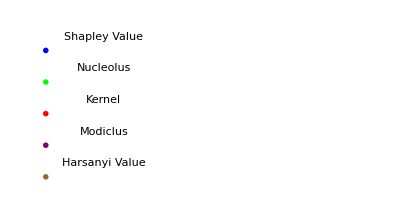

```mathematica
gr2=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewLegend->True]
```

A plot of the Lorenz solution can be drawn while setting the option “ViewPayoffSol→True” and “PayoffCoord→ lr” as it is shown by the next example.

```mathematica
gr3=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> lr]
```

-Graphics3D-

If we want to plot the equalitarian solution instead, we use the same options as above. However, we supply the latter option with the symbol that stores the equalitarian distribution.

```mathematica
gr4=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> fc]
```

-Graphics3D-

As suggested above, plotting the equalitarian and Lorenz solution can be achieved while using the same options as in the previous example with the difference that we now supply a list of solution vectors. This is shown next.

```mathematica
gr4b=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> {fc,lr}]
```

-Graphics3D-

Modiclus Plot

```mathematica
gr5=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord-> mnc]
```

-Graphics3D-

```mathematica
gr5a=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewLegend->True]
```

-Graphics-

Plotting Modiclus, Equalitarian, and Lorenz Solution

```mathematica
gr5b=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {fc,lr}]
```

-Graphics3D-

Plot Vector x2

```mathematica
gr6=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> x2]
```

-Graphics3D-

Plotting Modiclus, Equalitarian, Lorenz Solution, and Vector x2

```mathematica
gr6b=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {fc,lr,x2}]
```

-Graphics3D-

Plot Linear Combination of the Pre-Nucleolus and Lorenz Solution

```mathematica
gr7=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> lcb]
```

-Graphics3D-

Plotting Modiclus, Equalitarian, Lorenz Solution, Vector x2 and Vector lcb

```mathematica
gr8b=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {fc,lr,x2,lcb}]
```

-Graphics3D-

Plot Lorenz Set

In this example, we abuse the option that was designed for drawing a line segment of kernel in order to plot the Lorenz set while setting “KernelCoord→{lr,lcb}”.

```mathematica
gr9=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->{lr,lcb},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewPayoffSol->True,PayoffCoord-> lcb]
```

-Graphics3D-

Plotting all Vectors and Solutions

```mathematica
gr9b=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->{lr,lcb},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {fc,lr,x2,lcb}]
```

-Graphics3D-

Plotting Core Vertices and Lorenz Set

```mathematica
gr10=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->{lr,lcb},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewPayoffSol->True,PayoffCoord-> crv]
```

-Graphics3D-

Plotting Core Vertices, Lorenz Set and all Vectors

```mathematica
pts=FlattenAt[Append[crv,{fc,lr,x2,lcb}],6]
```

{{6,1,1,0},{7,0,0,1},{7,0,1,0},{7,1,0,0},{8,0,0,0},{2,2,2,2},{6,1,1,0},{13/2,1/2,1,0},{749/100,1/150,1/150,149/300}}

```mathematica
gr10b=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->{lr,lcb},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> pts]
```

-Graphics3D-

Checking core membership of some selected solutions can be accomplished with

```mathematica
BelongToCoreQ[ExpGame12,lr]
```

True

```mathematica
CoreElementsQ[ExpGame12,lr]
```

True

```mathematica
BelongToCoreQ[ExpGame12,mnc]
```

True

```mathematica
CoreElementsQ[ExpGame12,mnc]
```

True

```mathematica
BelongToCoreQ[ExpGame12,x2]
```

True

```mathematica
CoreElementsQ[ExpGame12,x2]
```

True

```mathematica
BelongToCoreQ[ExpGame12,lcb]
```

True

```mathematica
CoreElementsQ[ExpGame12,lcb]
```

True

#### Strong Epsilon Core

Here we provide some examples to draw the strong epsilon core in relation to some game solutions.

```mathematica
Options[StrongEpsCore3dV6]
```

{CriticalValue→{1},EpsStrValues→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowCore→True,ShowImputationSet→True,ShowStrongEpsCore→True,SyncDim→True,ViewKernelSol→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False}

```mathematica
g0=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,EpsStrValues->25]
```

-Graphics3D-

```mathematica
g1=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,EpsStrValues->15]
```

-Graphics3D-

```mathematica
g2=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,EpsStrValues->5]
```

-Graphics3D-

```mathematica
g3=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewPayoffSol->True,PayoffCoord-> lr,EpsStrValues->1]
```

-Graphics3D-

```mathematica
g3b=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> lr,EpsStrValues->1]
```

-Graphics3D-

```mathematica
g3c=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> lr,EpsStrValues->1]
```

-Graphics3D-

```mathematica
g4=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewPayoffSol->True,PayoffCoord-> {lr,fc},EpsStrValues->1]
```

-Graphics3D-

```mathematica
g5=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewPayoffSol->True,PayoffCoord-> {lr,fc},EpsStrValues->1/2]
```

-Graphics3D-

```mathematica
g6=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewPayoffSol->True,PayoffCoord-> {lr,fc},EpsStrValues->1/8]
```

-Graphics3D-

```mathematica
g7=StrongEpsCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewPayoffSol->True,PayoffCoord-> {lr,fc},EpsStrValues->-1/8]
```

-Graphics3D-

#### Weber Set

In this section, we demonstrate of how we can plot the Weber set of the game in relation to the above introduced game solutions or allocations. Five solutions, namely the Shapley value, the Harsanyi value, the nucleolus, a kernel element or a line segment of it, and the modiclus can be plotted while imposing an internal computation and drawing of graphics elements. If one wants to plot, for instance,  the Lorenz solution or any other allocation or a set of allocations, then one should use the options “ViewPayoffSol→True” and   “PayoffCoord-> payoffs”. Here the argument payoff indicates a sole imputation or a list of imputations. Notice that one needs to set the option “ViewPayoffSol” to true to visualize the supplied allocation, otherwise it will not be drawn. Similar for the four above mentioned solutions with the difference that one can supply an empty set to the “XXXCoord” option  whenever “ViewXXXSol” is set to true, then these solutions will be computed internally. Note that it is not possible to draw the core directly with the function devoted to the Weber set, instead one has to use the function "PlotCore3dV6".

The option set with its default values can be retrieved through

```mathematica
Options[PlotWeberSet3dV6]
```

{HarsanyiValCoord→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowImputationSet→True,SyncDim→True,Verbosely→True,ViewHarsanyiSol→False,ViewKernelSol→False,ViewLegend→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False,VRepresentation→False}

A simple graphic of the imputation set with the Weber set and some selected solutions can be drawn as follows:

```mathematica
wb1=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

In the next step, we want to draw ceteris paribus the Harsanyi value. However, the Harsanyi value is equal to the provided Shapley value, and it is drawn after the Shapley value, so it depicts the Harsanyi value graphic and the above solution is now drawn in blue rather than in brown.

```mathematica
wb2=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewHarsanyiSol->True,HarsanyiValCoord->harv]
```

-Graphics3D-

A Legend listing that mention some point solutions can be incorporated into the graphic while turning on the option “ViewLegend -> True”.

```mathematica
wb3=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewLegend->True]
```

-Graphics-

A plot of the marginal contribution vectors can be drawn while setting the option “ViewPayoffSol→True” and “PayoffCoord→ mrgv2” as it is shown by the next example.

```mathematica
wb4=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> mrgv2]
```

-Graphics3D-

If we want to plot the equalitarian instead, we use the same options as above. However, we supply the latter option with the symbol that stores the equalitarian distribution.

```mathematica
wb5=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> fc]
```

-Graphics3D-

Even with the Weber set, the modiclus can be depicted.

```mathematica
wb6=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord-> mnc]
```

-Graphics3D-

Note that the Modiclus is close to the nucleolus, and the computed pre-kernel element, we turn them off. But enlarge now the figure size.

```mathematica
wb7=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->False,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord-> mnc,PictureSize->{800,868}]
```

-Graphics3D-

The drawing of Weber set presented so-far depends on the HRepresentation (hyperplane representation). It is also possible to switch to a VRepresentation (vertex representation).

```mathematica
wb8=PlotWeberSet3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord-> mnc,VRepresentation->True]
```

-Graphics3D-

This produces a different skeleton of the Weber set. However, under some circumstances it may be defective. Thus, we recommend to use the HRepresentation instead since it is more reliable unless one has good reason for switching the representation, for instance, for verifying the plot.

Finally, we want to demonstrate of how one can depict the Weber set in connection with the core. For doing so, we have to refer again to the function "PlotCore3V6" while invoking the option "ShowWeberSet -> True".

```mathematica
wb9=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord-> mnc,VRepresentation->True,ShowWeberSet->True]
```

-Graphics3D-

Thus, to plot the core vertices and the Lorenz set in connection with the Weber set one has to execute

```mathematica
wb10=PlotCore3dV6[ExpGame12,ViewKernelSol->True,KernelCoord->{lr,lcb},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->pn,ViewModiclusSol->True,ModiclusCoord-> mnc,VRepresentation->False,ShowWeberSet->True,ViewPayoffSol->True,PayoffCoord-> crv]
```

-Graphics3D-

#### Kernel Catchers

In this section, we shall see how to plot several kernel catchers in relation to the core and the above introduced game solutions.

```mathematica
Options[ShowKernelCatcherV6]
```

{CriticalValue→{1},EpsStrValues→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowCore→False,ShowImputationSet→True,ShowLowerSet→False,ShowStrongEpsCore→False,ShowUpperSet→True,SyncDim→True,ViewKernelSol→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False}

```mathematica
k0=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->False,ShowUpperSet->True,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k0a=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->False,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k0b=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->False,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k0c=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k0d=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k0e=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k1=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewPayoffSol->True,PayoffCoord-> {lr,fc}]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k1a=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {lr,fc}]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

```mathematica
k1b=ShowKernelCatcherV6[ExpGame12,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {lr,fc}]
```

Is core nonempty? True

Lower Set is a unique point.

Lower Point is plotted as a orange point!

-Graphics3D-

#### Animate Geometric Property of the Kernel/Nucleolus

Finally, we provide an example to run an animation.

```mathematica
Options[AnimationKernelPropertyV6]
```

{CriticalValue→{1},EpsStrValues→{},KernelCoord→{},LowerCriticalVal→{},ManipulateMode→False,ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowCore→True,ShowImputationSet→True,ShowStrongEpsCore→True,StepSize→{-1/4},SyncDim→True,UpperCriticalVal→{1/2},ViewKernelSol→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False}

```mathematica
EpsCore[ExpGame12]
```

{-1/3,{x[1]→7,x[2]→1/3,x[3]→1/3,x[4]→1/3,e→0,TUG`TuGames`Private`f→1/3}}

```mathematica
{time1,a1}=AbsoluteTiming[AnimationKernelPropertyV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {lr,fc},UpperCriticalVal->{25},LowerCriticalVal->{},CriticalValue->{1},StepSize->{-(1/10)},ShowImputationSet->True,ShowCore->True]];
```

```mathematica
time1
```

2.95696

```mathematica
Length[a1]
```

254

```mathematica
ListAnimate[a1,1]
```

```mathematica
{time2,a2}=AbsoluteTiming[AnimationKernelPropertyV6[ExpGame12,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,ViewPayoffSol->True,PayoffCoord-> {lr,fc},UpperCriticalVal->{25},LowerCriticalVal->{-1/3},CriticalValue->{1},StepSize->{-(1/20)},ShowImputationSet->True,ShowCore->True,ManipulateMode->True]];
```

```mathematica
time2
```

0.000791

The next symbol, we have to reevaluate to impose an animation.

```mathematica
a2
```

| Related Guides
▪TUGFunctionsIndex

| Related Tech Notes
▪Manual TuGames
▪ParaTuGames Package
▪Graphics 2D
▪Graphics 3D